To see an animation of multiplayer model go to showing random move section

### Backdoor pass 2D

TODO: Make defender ring accurate, my idea is to use distance from passer. Right now it uses the time when the ball passes the defender

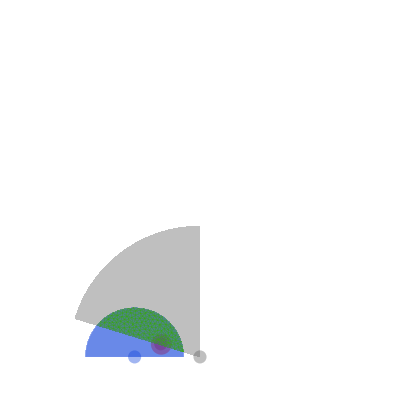

```mathematica
Module[{passerPosition, attackerPositions, defenderPositions,playerSize, offenseSpeed, defenseSpeed, ballSpeed, reactionTime, maxPassDecisionTime, maxBallInAirTime, attackerDisks, perpindicularPassLine, intersectionPoint, interceptionWindow, defenderDisks, defenseRangeDisk, passLine, passRangeDisk, attackerRangeDisk, passerToDefenderAngle, passerDisk, halfcourt, passArea, discreteRegion, discretePassArea},

passerPosition= {0, 1};attackerPositions = {{-10, 1}};defenderPositions = {{-6, 3}};playerSize = 1;
offenseSpeed = 1.5;defenseSpeed = 1;ballSpeed = 4;reactionTime = 1;maxPassDecisionTime = 2;
maxBallInAirTime = 3;halfcourt=Rectangle[{-25,0},{25,50}];
passerDisk = Disk[passerPosition, playerSize];
attackerDisks = Map[Disk[#, playerSize]&, attackerPositions];
defenderDisks = Map[Disk[#, playerSize]&, defenderPositions];
perpindicularPassLine = Round/@Line[{defenderPositions[[1]], AngleVector[defenderPositions[[1]],{20, Pi/4}]}];
intersectionPoint = ResourceFunction["LineIntersection"][passLine, perpindicularPassLine];
interceptionWindow = EuclideanDistance[passerPosition, intersectionPoint]/ballSpeed ;
defenseRangeDisk = Disk[defenderPositions[[1]], EuclideanDistance[defenderPositions[[1]], passerPosition]*defenseSpeed /ballSpeed];
passLine  = Round/@Line[{passerPosition, AngleVector[passerPosition,{ballSpeed*(maxPassDecisionTime+maxBallInAirTime),3Pi/4}]}];
passerToDefenderAngle = Pi -VectorAngle[{defenderPositions[[1, 1]], 1}, defenderPositions[[1]]];
passRangeDisk = Disk[passerPosition, ballSpeed*(maxPassDecisionTime+maxBallInAirTime) , {Pi/2, passerToDefenderAngle}];
attackerRangeDisk = Disk[attackerPositions[[1]], offenseSpeed*(maxPassDecisionTime+maxBallInAirTime), {Pi, 0}];
passArea = BooleanRegion[#1&&#2&,{passRangeDisk,Disk[{-10,1},7.5]}];
discretePassArea=DiscretizeRegion[passArea];
Graphics[{White, halfcourt, defenderColor,Opacity[0.4],defenderDisks,attackerColor,attackerDisks,attackerRangeDisk, neutralColor, passerDisk,defenderColor,defenseRangeDisk,  neutralColor, passRangeDisk, attackerColor, Opacity[0.4], attackerRangeDisk, successColor,Opacity[0.4],MeshPrimitives[discretePassArea,2]}]
]
```

### Multiplayer 2D Graphics Model

#### Functions

```mathematica
getPoint[center_,angle_,radius_]:=center+radius*AngleVector[angle]
edgeToLine[edge_]:= Line[{edge[[1]], edge[[2]]}]
getAwayPoints[homePoints_, homeAwayDistance_:1/10]:= Map[{#[[1]],#[[2]] + homeAwayDistance}&, homePoints]

getHexRow[startPoint_, rowLength_]:= NestList[getPoint[#, 60Degree, 1]&, startPoint, rowLength];

getHomePoints[length_]:=Module[{hexRowLengths,startPoint, hexStartPointsLeft, hexStartPointsBottom, startPoints, allPoints},
hexRowLengths = Join[Range[length, 2length], Range[2length - 1, length, -1]];
startPoint = {0, 0};
hexStartPointsLeft = NestList[getPoint[#, -60Degree, 1]&, startPoint, length];
hexStartPointsBottom = NestList[getPoint[#, 0Degree, 1]&, getPoint[Last@hexStartPointsLeft, 0Degree, 1], length - 1];
startPoints= Join[hexStartPointsLeft, hexStartPointsBottom];
allPoints = Flatten[MapThread[getHexRow[#1, #2]&, {startPoints, hexRowLengths}], 1]
]

getRecPoints[point_, size_]:={getPoint[point, 225Degree, size], getPoint[point, 45Degree, size]}
getTriPoints[point_, size_]:=
{getPoint[point, 88Degree, size - 1/12],getPoint[point, 210 Degree, size], getPoint[point, 330Degree, size ]}

getBallLocation[team_,possessor_]:= Module[{shape},
shape=  
If[team == "home", 
Rectangle@@getRecPoints[homePlayers[[possessor]], playerSize],
Polygon[getTriPoints[awayPlayers[[possessor]], playerSize]]];
RegionCentroid[shape]
]
showGame[{homePlayers_, awayPlayers_ , ballLoc_, turn_}]:=Module[{hpRecs, apTris, allShapes, dribbler,ball},
hpRecs = Rectangle@@getRecPoints[#, playerSize]&/@ homePlayers;apTris = N/@Polygon@getTriPoints[#,playerSize]&/@ awayPlayers;
ball = Disk[ballLoc, ballSize];
background = Rectangle[{-1, -2}, {5, 2}];
Graphics[{FaceForm@White,background, EdgeForm@Black, FaceForm@White, gamePoly, FaceForm@Blue, hpRecs,FaceForm@Red ,apTris, Green, ball}]
]
getPlayerLoc[team_, i_]:= If[team == "home", homePlayers[[i]], awayPlayers[[i]]]

getLegalMoves[currentPoint_, speed_:1]:=Module[{allPoints},
  allPoints = Map[getPoint[currentPoint, #, speed]&, directions];
  Select[allPoints, RegionMember[gamePoly, #]&]
]

getTeamMove[{homePlayers_, awayPlayers_ , ballLoc_, turn_}]:= Module[{dribbler, players, offBallMoves, offBallRandomMoves, 
dribblerLoc, dribbleMoves, passBallLocs, passMoves, dribblerAllMoves, dribblerRandom, playersMoved}, 
If[turn == "α", players = homePlayers, players = awayPlayers];
offBallMoves = getLegalMoves/@ DeleteCases[players, ballLoc];
offBallRandomMoves = RandomChoice/@ offBallMoves;
dribbleMoves = {#, #}&/@getLegalMoves[ballLoc];
passBallLocs = Flatten[getLegalMoves[ballLoc, #]&/@ Range[ballSpeed, 1, -1], 1];
passMoves = {ballLoc, #}&/@ passBallLocs;
dribblerAllMoves  =Join[dribbleMoves, passMoves];
dribblerRandom = RandomChoice@dribblerAllMoves;
playersMoved = {dribblerRandom[[1]], offBallRandomMoves[[1]],offBallRandomMoves[[2]]};
{playersMoved, awayPlayers,dribblerRandom[[2]], Replace[turn, {"α"->"β","β"->"α"}]}
]


getObjectMovementFrames[start_, end_, frames_:5]:= Subdivide[start, end,frames]

showMove[gameStateStart_, gameStateEnd_, frameRate_:10]:= Module[{go1, go2, gf1, gf2, turn, hpl, apl, objectFrames, gameStatesFlat, 
gameObjectFrames, gameStates, graphicsFrames}, 
  go1 = gameStateStart[[;;2]];
  go2 = gameStateEnd[[;;2]];
  gf1 = Append[Flatten[go1, 1], gameStateStart[[3]]];
  gf2 = Append[Flatten[go2,1], gameStateEnd[[3]]];
  turn = Last@gameStateStart;
  Column[objectFrames = MapThread[getObjectMovementFrames[#1, #2, frameRate]&, {gf1, gf2}]];
  gameStatesFlat = Transpose[objectFrames];
  hpl = Length@homePlayers; apl = Length@awayPlayers;
  gameObjectFrames = {#[[;;hpl]], #[[hpl+1;;hpl+apl]],#[[hpl+apl+1]]}&/@ gameStatesFlat;
  gameStates = Append[#, turn]& /@ gameObjectFrames;
  Row[graphicsFrames = showGame/@ gameStates];
  ListAnimate[graphicsFrames, DefaultDuration->2, AnimationRepetitions->1]
  ]
```

#### Court

```mathematica
courtLength = 2;
directions = NestList[#+60Degree&, 0Degree, 5];
gamePoly = BoundingRegion[allLocs, "MinConvexPolygon"];
homeLocs = getHomePoints[courtLength];
awayLocs = getAwayPoints[homeLocs];
allLocs = Join[homeLocs, awayLocs];
homeEndZoneY = homeLocs[[courtLength+1, 2]] ;
awayEndZoneY = awayLocs[[-(courtLength+1), 2]];
```

#### Object Parameters

```mathematica
playerSize = 1/5;
ballSize = 1/12;
playerSpeed = 1;
ballSpeed= 2;
```

#### Initialization

α

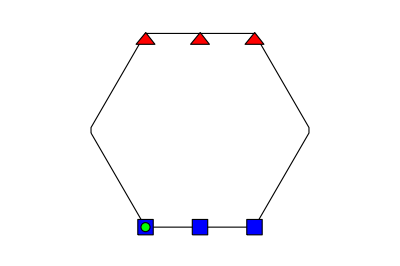

```mathematica
homePlayers = homeLocs[[{8, 13, 17}]];
awayPlayers = homeLocs[[{3, 7, 12}]];
allPlayers = Join[homePlayers, awayPlayers];
turn = "α"
dribbler = 1;
ballLoc = getPlayerLoc["home", dribbler];
initialGameState = {homePlayers, awayPlayers, ballLoc, turn};
showGame[initialGameState]
```

#### Showing Gameplay

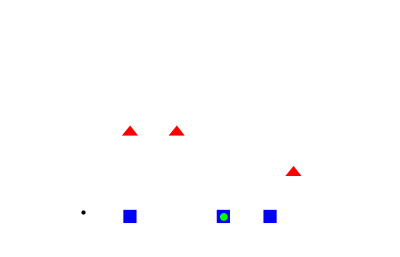

### Styling

```mathematica
getColorInputForm[color_]:=InputForm@RGBColor@color
```

```mathematica
ColorSetter[Dynamic[offensiveColor]]
```

$CellContext`offensiveColor

```mathematica
getColorInputForm[offensiveColor]
```

RGBColor[0.0861371786068513, 0.27838559548332953, 0.8631418326085298]

```mathematica
attackerColor =RGBColor[0.0861371786068513,0.27838559548332953,0.8631418326085298]
```

RGBColor[0.0861371786068513, 0.27838559548332953, 0.8631418326085298]

```mathematica
ColorSetter[Dynamic[defensiveColor]]
```

$CellContext`defensiveColor

```mathematica
defenderColor =RGBColor[0.8807965209430075,0.,0.04405279621576257]
```

RGBColor[0.8807965209430075, 0., 0.04405279621576257]

```mathematica
ColorSetter[Dynamic[successColor]]
```

$CellContext`successColor

```mathematica
successColor = RGBColor[0.2174563210498207,0.6534676127260243,0.06826886396581978]
```

RGBColor[0.2174563210498207, 0.6534676127260243, 0.06826886396581978]

```mathematica
ColorSetter[Dynamic[neutralColor]]
```

$CellContext`neutralColor

```mathematica
getColorInputForm[neutralColor]
```

RGBColor[0., 0., 0.]

```mathematica
neutralColor = RGBColor[0.37752346074616616,0.37750820172426947,0.37750820172426947]
```

RGBColor[0.37752346074616616, 0.37750820172426947, 0.37750820172426947]

```mathematica
ColorSetter[Dynamic[coveredColor]]
```

$CellContext`coveredColor

```mathematica
coveredColor = RGBColor[0.4669565880827039,0.07298390173189899,0.5677576867322804]
```

RGBColor[0.4669565880827039, 0.07298390173189899, 0.5677576867322804]

RGBColor[0.4669565880827039, 0.07298390173189899, 0.5677576867322804]